-Graphics-

-Graphics-
-Graphics-

-Graphics-

```mathematica
length=150;
```

## Hamiltonian

```mathematica
matH=Table[0,{i,1,length},{j,1,length}];
```

```mathematica
%//MatrixForm;
```

```mathematica
(*Table[matH[[i,i]]=1,{i,length/2+1,length}];*)

For[i=1,i<length/2+1,i++,matH[[i,i]]=0];
For[i=length/2+1,i<length+1,i++,matH[[i,i]]=1];
(*matH//MatrixForm*)
```

```mathematica
(*randomI=Table[0.01 RandomReal[],{i,1,100},{j,1,100}];*)
randomI=Table[0,{i,1,length},{j,1,length}];Table[randomI[[i,j]]=RandomVariate[NormalDistribution[0,0.01]],{i,1,length},{j,i+1,length}];
```

```mathematica
intH=matH+randomI+Transpose[randomI];
(*MatrixForm[intH]*)
```

```mathematica
(*timestep=.0001;*)
```

## Initial state

```mathematica
(*initialstate=ConstantArray[0,100];initialstate[[1]]=1;*)
```

```mathematica
initialstate=ConstantArray[0,length]; (*0 means the amount of the elements. Not the start point of the elements!*)
initialstate[[1]]=0.15^(1/2);
initialstate[[length/2+1]]=0.85^(1/2);

(*initialstate//MatrixForm*)
(*MatrixForm[initialstate]*)
```

```mathematica
(*initialstate=ConstantArray[0,100];For[i=1,i<51,i++,initialstate[[i]]=.15^(1/2)];For[i=51,i<101,i++,initialstate[[i]]=.85^(1/2)];*)
```

## Time evolution of the state

```mathematica
(*phi[t_]:=MatrixExp[-I t intH].initialstate;*)
phi[t_]:={MatrixExp[-I t intH,initialstate]}//Transpose;
(*we put MatrixExp in the {} in order to make the array as a row vector. Then after that we use Transpose to convert it as a calumn vector*)

phistar[t_]:=Conjugate[phi[t]]//Transpose;
```

General::munfl: 1.42537×10^-165 1.4187×10^-170 is too small to represent as a normalized machine number; precision may be lost.

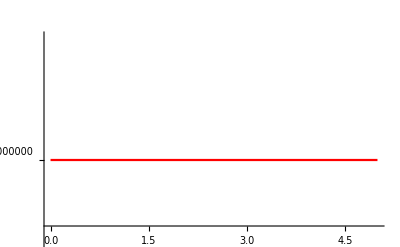

```mathematica
Plot[Norm[phi[t]],{t,0,5},PlotStyle->Red]
```

## Density matrix

```mathematica
rho[t_]:=Flatten[Chop[Outer[Times,phi[t],phistar[t]],0.00001],2];
```

## Reduced density matrix

```mathematica
rhoR[t_]:=Map[Tr,Partition[rho[t],{length/2,length/2}],{2}];

rhoR[1]//MatrixForm
```

(0.148768 | 0.196506+0.286541 ⅈ
0.196506-0.286541 ⅈ | 0.851089)

```mathematica
eigenR[t_]:=Chop[Eigenvalues[rhoR[t]]];
```

General::munfl: 1.42537×10^-165 1.4187×10^-170 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

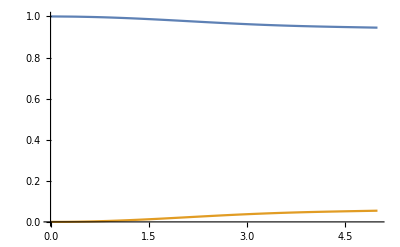

```mathematica
Plot[{eigenR[t][[1]],eigenR[t][[2]]},{t,0,5}]
```

## Entropy

```mathematica
(*entropia de von newman*)
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

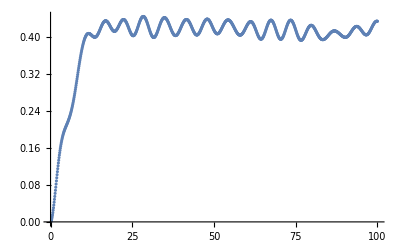

```mathematica
entropy[t_]:=Total[Chop[-eigenR[t]* Log[eigenR[t]]]];
(*S[t_]:=Entropy[eigenR[t]];*)

(*entropy[t_]:=-Sum[r[[i]] Log[r[[i]]],{i,Length[r]}]*)
data=ParallelTable[{t,entropy[t]},{t,0,100,.1}];
ListPlot[data,PlotRange->All]
```